```mathematica
SetDirectory["/home/zah/github/OQSID-thesis/MODELS"];
Directory[]
(*A = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/A"];*)
(*Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/Ac"];*)
(* gamma = 0.0 0.079477 0.25133 0.79477 2.5133 7.9477 25.133 79.477 251.33*)
Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.25133/Ac"]

Subscript[b, x] :={1, 0, 0, 1}ᵀ;
Subscript[Ac, symb]= ({{-γ/2, ω, 0, 0}, {-ω, -γ/2, 0, 0}, {0, 0, -γ, γ}, {0, 0, 0, 0}});
ℐ[n_]:=IdentityMatrix[n];
TransferFunction[A_, b_]:= Assuming[{γ∈Reals,ω∈Reals},Simplify[Inverse[s*ℐ[4]- A].b]];
```

/home/zah/github/OQSID-thesis/MODELS

{{-5.45125×10^-8,25.1501,-0.00533117,-2.28992×10^-14},{-25.1327,-0.251386,-0.000621224,4.77622×10^-14},{0.0000563978,-0.000348851,-0.251773,7.86491×10^-14},{3.23583×10^-6,1.72616×10^-6,0.251014,-7.8412×10^-14}}

```mathematica
Subscript[Gx, symb] =TransferFunction[Subscript[Ac, symb], Subscript[b, x] ];
Subscript[Gx, SID]=TransferFunction[Subscript[Ac, SID], Subscript[b, x] ];
```

```mathematica
eqv[p_]:=p==0;
eqvs :=Map[eqv, Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]]]
MatrixForm[eqvs ];
```

```mathematica
Solve[eqvs]
```

{}

```mathematica
Solve[{eqvs[[9]],eqvs[[10]]}]
```

{{γ→0.251386,ω→25.1327}}

```mathematica
obj:=
Total[(Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]])^2]
```

```mathematica
NMinimize[obj, {γ,ω}]
```

{6.50449×10^6,{γ→-0.377906,ω→-0.00208867}}

```mathematica
Show[Plot3D[Log[obj], {γ,-1,1}, {ω,-10,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality"]
```

-Graphics3D-

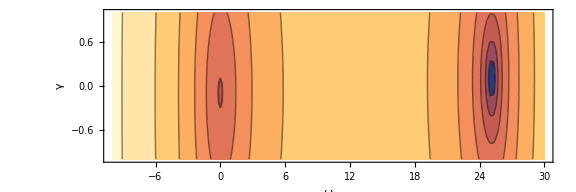

```mathematica
Show[ContourPlot[Log[obj], {ω,-10,30},{γ,-1,1}, Axes->True,AxesLabel ->{ω,γ} ,LabelStyle-> Bold,AspectRatio->1/3],ImageSize -> Large,PerformanceGoal->"Quality"]
```